```mathematica
SetDirectory["/home/jamie/simionwork/Vdists"];
files = Flatten /@ Import /@ Table[ToString[v] <> ".dat",{v,50,100,5}];
```

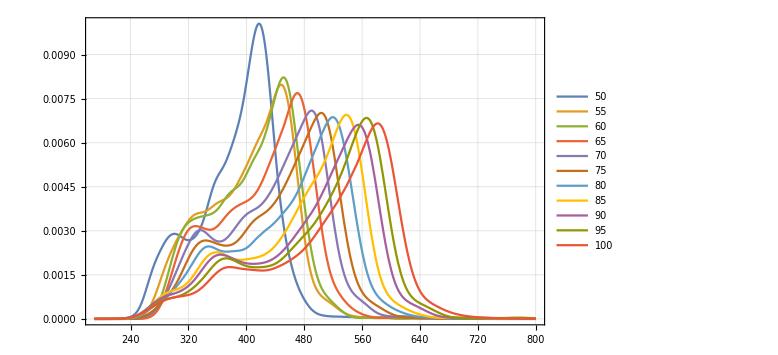

```mathematica
dists = PDF[SmoothKernelDistribution[#],x]&/@files;
Plot[dists,{x,190,800},ImageSize->Large,PlotTheme->"Detailed",PlotLegends->Range[50,100,5]]
```

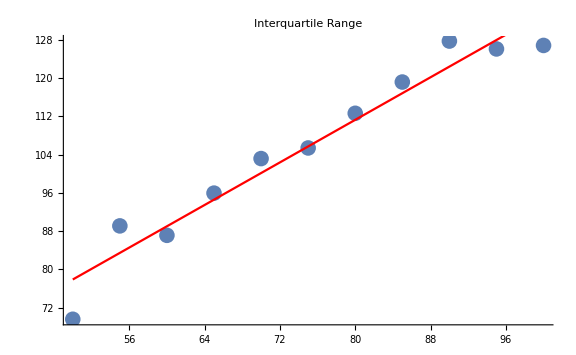

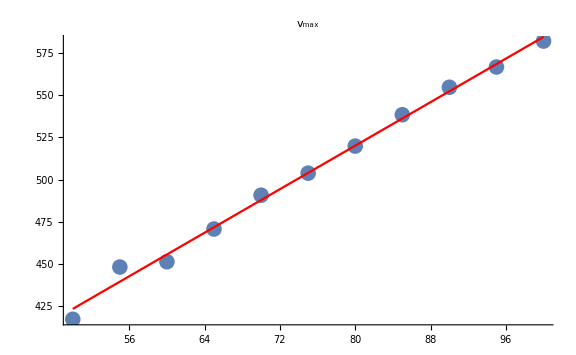

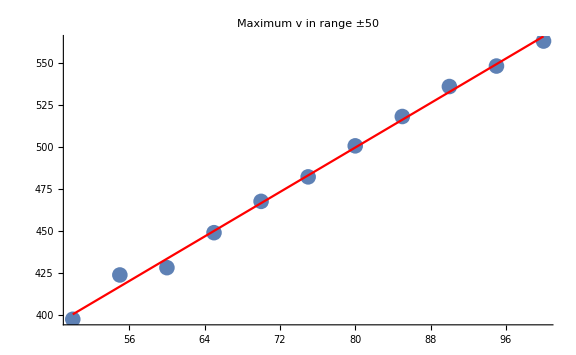

```mathematica
findfIQR = Fit[Transpose@{Range[50,100,5],InterquartileRange/@files},{1,x},x];
findfMode = Fit[Transpose@{Range[50,100,5],Quiet@FindArgMax[#,{x,500}]&/@dists // Flatten},{1,x},x];
findfRange = Fit[Transpose@{Range[50,100,5],z/.Quiet@FindRoot[Evaluate[#/.x->z-50]==Evaluate[#/.x->z+50],{z,Quiet@FindArgMax[#,{x,500}][[1]]}]&/@dists},{1,x},x];
Show[{ListPlot[Transpose@{Range[50,100,5],InterquartileRange/@files}],Plot[findfIQR,{x,50,100},PlotStyle->Red]},ImageSize->Large,PlotLabel->"Interquartile Range"]
Show[{ListPlot[Transpose@{Range[50,100,5],Quiet@FindArgMax[#,{x,500}]&/@dists // Flatten}],Plot[findfMode,{x,50,100},PlotStyle->Red]},PlotLabel->"v_max"]
Show[{ListPlot[Transpose@{Range[50,100,5],z/.Quiet@FindRoot[Evaluate[#/.x->z-50]==Evaluate[#/.x->z+50],{z,Quiet@FindArgMax[#,{x,500}][[1]]}]&/@dists}],Plot[findfRange,{x,50,100},PlotStyle->Red]},PlotLabel->"Maximum v in range ±50"]
```

```mathematica
Manipulate[Show[{Plot[dists[[5]],{x,200,600},ImageSize->Large,GridLines->{{z},{}}],Graphics[{PointSize[Large],Point[{z+50,dists[[5]]/.x->z+50}],Point[{z-50,dists[[5]]/.x->z-50}],Line[{{z+50,dists[[5]]/.x->z+50},{z-50,dists[[5]]/.x->z-50}}],Text[NIntegrate[dists[[5]],{x,z-50,z+50}],{250,0.007}]}]}],{z,200,600}]
```

Part::partd: Part specification dists ⟦ 5 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NIntegrate::inumr: The integrand dists ⟦ 5 ⟧ has evaluated to non-numerical values for all sampling points in the region with boundaries {{150, 250}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

Part::partd: Part specification dists ⟦ 5 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NIntegrate::inumr: The integrand dists ⟦ 5 ⟧ has evaluated to non-numerical values for all sampling points in the region with boundaries {{150, 250}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

Part::partd: Part specification dists ⟦ 5 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NIntegrate::inumr: The integrand dists ⟦ 5 ⟧ has evaluated to non-numerical values for all sampling points in the region with boundaries {{150, 250}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

Part::partd: Part specification dists ⟦ 5 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NIntegrate::inumr: The integrand dists ⟦ 5 ⟧ has evaluated to non-numerical values for all sampling points in the region with boundaries {{150, 250}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

Part::partd: Part specification dists ⟦ 5 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NIntegrate::inumr: The integrand dists ⟦ 5 ⟧ has evaluated to non-numerical values for all sampling points in the region with boundaries {{150, 250}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

```mathematica
Solve[findfRange == 500]
```

{{x→80.0853}}

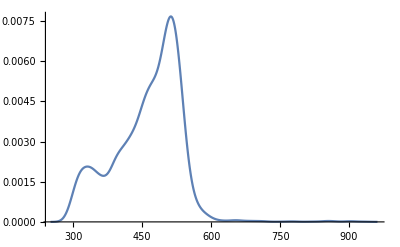

```mathematica
SmoothHistogram[Import["../vOut.dat"][[1]]]
single = Import["../vOut.dat"][[1]];
```

```mathematica
z/.Quiet@FindRoot[Evaluate[#/.x->z-50]==Evaluate[#/.x->z+50],{z,Quiet@FindArgMax[#,{x,500}][[1]]}]&@PDF[SmoothKernelDistribution[Import["../vOut.dat"][[1]]],x]
InterquartileRange@Import["../vOut.dat"][[1]]
```

491.64

97.411

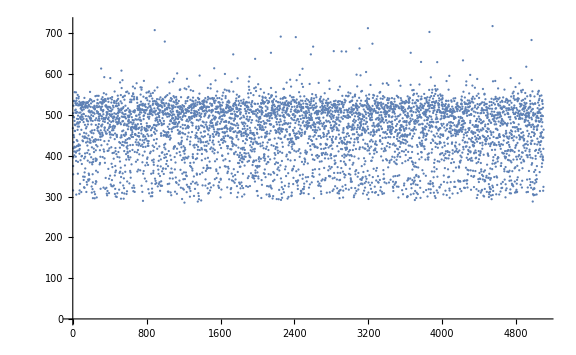

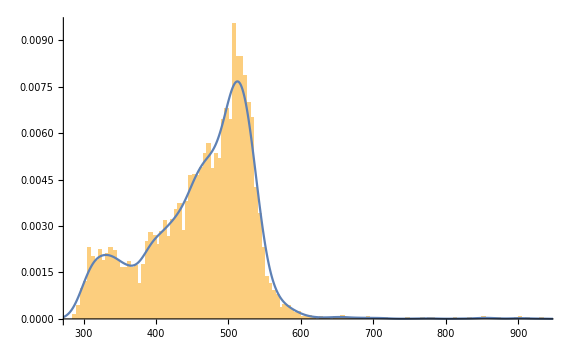

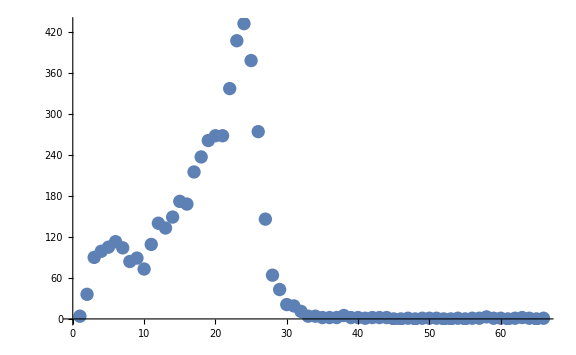

```mathematica
ListPlot[single,ImageSize->Large]
Show[{Histogram[single,100,"PDF"],SmoothHistogram[single]}]
ListPlot@BinCounts[single,10]
```